Približna vrednost π: 3.1436

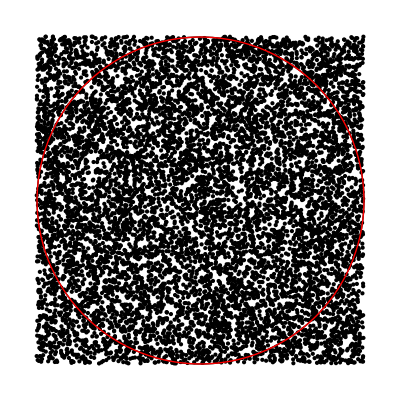

```mathematica
Get["C:\\Users\\anzez\\OneDrive\\Namizje\\Faks\\3. Letnik\\NRO\\2_Domača_naloga\\montecarlo_dodatek.m"]

(*Monte Carlo*)
n=10000; (*Število simuliranih točk*)
priblPi=MonteCarloPiSimulation[n];

(*približna vrednost π*)
Print["Približna vrednost π: ",N[priblPi]]

Graphics[{Circle[],PointSize[Small],Point[RandomReal[{-1,1},{n,2}]],Red,Circle[{0,0},1]}]
```